# Managing thermal guild interactions in warming food webs

NOTE TO SELF: ENDED OFF COPYING AND PASTING THE OTHER PARAM SET. SO CONTINUE OFF FROM THERE WHEN IT’S TIME.

## NOTES

> This is the cleaned up version of “Thermal niche management_LJ_param_set_01_09_21_P2onJ_openupunexpectedspace”
> “Thermal niche management_LJ_param_set_01_09_21_JClowerattack” is the alternate result (not yet incorporated in this NB), but can be done easily by changing parameters (which I have provided in the notes in the “Parameters” section
>  this notebook has piecewise exponential mortality, with σ2 = 1 (in temp-dependent mortality function) which makes the increase steeper, and m=0.001 or m=0.002 (to keep m within a reasonable range...similar to FB4).

## Initialization

## Model

tyler had different attack rate for walleye on new resource (RA1), but didn’t add it to params list, so I added it to params list, but kept it the same as others (to start)

```mathematica
Clear[fR1,fR2,fJ1,fA1,fA2,fRA1]
fR1[R1_,R2_,J1_]:= rmax*R1(1-R1/K1)- awj1*(Piecewise[{{Exp[-((T1-Topt2)/(2 σ))^2],T1<Topt2},{1-((T1-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>T1≥Topt2},{0,T1≥Tmax2}}])*R1*J1-ar21*(Piecewise[{{Exp[-((T1-Topt4)/(2 σ))^2],T1<Topt4},{1-((T1-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>T1≥Topt4},{0,T1≥Tmax4}}])*R1*R2 
fR2[R1_,R2_,A1_,A2_]:= ar21*(Piecewise[{{Exp[-((T1-Topt4)/(2 σ))^2],T1<Topt4},{1-((T1-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>T1≥Topt4},{0,T1≥Tmax4}}])*R1*R2-awa1*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*R2*A1 - aba1*(Piecewise[{{Exp[-((T1-Topt3)/(2 σ))^2],T1<Topt3},{1-((T1-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T1≥Topt3},{0,T1≥Tmax3}}])*R2*A2 - (Piecewise[{{mR21*T1,T1≤10},{mR21*T1+mR21*Exp[((T1-Tmax4)/σ2)],10<T1}}])*R2
fJ1[R1_,R2_,J1_,A1_,A2_]:= (αw2*(1-som)*awa1*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*R2*A1)/(1+βw1*(1-som)*awa1*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*R2*A1)+ (1-mat)*(awj1*(Piecewise[{{Exp[-((T1-Topt2)/(2 σ))^2],T1<Topt2},{1-((T1-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>T1≥Topt2},{0,T1≥Tmax2}}])*R1*J1) - aba2*(Piecewise[{{Exp[-((T1-Topt3)/(2 σ))^2],T1<Topt3},{1-((T1-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T1≥Topt3},{0,T1≥Tmax3}}])*J1*A2 - (Piecewise[{{mj1*T1,T1≤10},{mj1*T1+mj1*Exp[((T1-Tmax2)/σ2)],10<T1}}])*J1
fA1[R1_,R2_,J1_,A1_,RA1_]:= mat*(awj1*(Piecewise[{{Exp[-((T1-Topt2)/(2 σ))^2],T1<Topt2},{1-((T1-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>T1≥Topt2},{0,T1≥Tmax2}}])*R1*J1) + som*awa1*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*R2*A1 + som*awax*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*RA1*A1 - (Piecewise[{{ma1*T1,T1≤10},{ma1*T1+ma1*Exp[((T1-Tmax1)/σ2)],10<T1}}])*A1 
fA2[R2_,A2_,J1_]:= aba1*(Piecewise[{{Exp[-((T1-Topt3)/(2 σ))^2],T1<Topt3},{1-((T1-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T1≥Topt3},{0,T1≥Tmax3}}])*R2*A2 + aba2*(Piecewise[{{Exp[-((T1-Topt3)/(2 σ))^2],T1<Topt3},{1-((T1-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T1≥Topt3},{0,T1≥Tmax3}}])*J1*A2 - (Piecewise[{{mAb1*T1,T1≤10},{mAb1*T1+mAb1*Exp[((T1-Tmax3)/σ2)],10<T1}}])*A2 - h*A2
fRA1[A1_,RA1_]:= rmax2*RA1 (1-RA1/K2)- awax*(Piecewise[{{Exp[-((T1-Topt1)/(2 σ))^2],T1<Topt1},{1-((T1-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T1≥Topt1},{0,T1≥Tmax1}}])*RA1*A1
```

```mathematica
Clear[PdSystem]
PdSystem[{R10_, R20_, J10_, A10_, A20_, RA10_}] := {
 R1'[t]== fR1[R1[t],R2[t],J1[t]],
 R2'[t]== fR2[R1[t],R2[t],A1[t],A2[t]],
 J1'[t]== fJ1[R1[t],R2[t],J1[t],A1[t],A2[t]],
 A1'[t]== fA1[R1[t],R2[t],J1[t],A1[t],RA1[t]], 
 A2'[t]== fA2[R2[t],A2[t],J1[t]],
 RA1'[t]== fRA1[RA1[t],A1[t]],
 R1[0]==R10, 
 R2[0]==R20, 
 J1[0]==J10, 
 A1[0]==A10, 
 A2[0]==A20,
 RA1[0]== RA10
 };
```

## Parameters

Here, “rates” are the temperature-independent variables and “params” are the base values for the temperature-dependent variables. NOTE that I switched scenarios 1 and 2. so the new scenario 1 will have rates2 and params2 because it use to be scenario 1. However, this is consistent with the TPCs and the “Scenario 1” and “Scenario 2” sections, so just leave it for now.

### Parameters for Scenario 1 (main): P_1 and P_2 lower base attack rate

```mathematica
Clear[rates, params]
rates = Dispatch[{
som -> 0.8,
mat -> 0.65, (*65*)
αw2 -> 1.0,
βw1 -> 0.0025, (*can use 0.0025 like Ogle 2013 (fishR) and get the same result - tested in "betatest" notebook---used 1.0 before with same results*)
rmax -> 1,
K1 -> 10,
h -> 0,
K2 -> 1 (*changing this to 10 makes it so that there is no difference between bass presence/absence on the walleye population. Probably because walleye have enough resources regardless of trophic control*),
rmax2 -> 1
(*v1 -> 0.3,
u1 -> 0.3,
h1 -> 0, (*Subscript[R, 2] harvest*)*)
}];

(*for TPC functions*)
params = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

awax -> 0.001,
awa1 -> 0.04, (*adult wal attack on R2, FB4 0.0387*)
awj1 -> 0.09, (*juv wal attack on resource, FB4 0.13*)
ar21 -> 0.09, (*R2 attack on resource, FB4 0.052*)
aba1 -> 0.04, (*bass attack on R2, FB4 0.035*)
aba2 -> 0.0, (*bass attack on juv wal*)

ma1 -> 0.001, (*, alt 0.85*)
mj1 -> 0.002, (*, alt 0.85*)
mAb1 -> 0.001, (*, alt 0.85*)
mR21 -> 0.002, (*, alt 0.85*)

Topt1 -> 22, (*adult wal 22- A1*)
Topt2 -> 25, (*juv wal 25- J1*)
Topt3 -> 27.5, (*largemouth bass, smallmouth would be 29- A2*)
Topt4 -> 27, (*bluegill 27- R2*)

Tmax1 -> 28, (*28*)
Tmax2 -> 28, (*28 main pater says 28, but high range is 35*)
Tmax3 -> 37, (*smallmouth would be 36*)
Tmax4 -> 36, (*36*)

T1->25
}];
```

### Parameters for Scenario 2: P_1 and P_2 higher base attack rate - Don’t run this if you’ve run scenario 1 params above

NOTE :  Running below code will yield the alternate - “expected” - result discussed in the MS (the result that is included in the supplementary material, Figs. S3 & S4)

```mathematica
Clear[rates, params]
rates = Dispatch[{
som -> 0.8,
mat -> 0.65, (*65*)
αw2 -> 1.0,
βw1 -> 0.0025, (*can use 0.0025 like Ogle 2013 (fishR) and get the same result - tested in "betatest" notebook---used 1.0 before with same results*)
rmax ->0.5,
K1 -> 5,
h -> 0,
K2 -> 1 (*changing this to 10 makes it so that there is no difference between bass presence/absence on the walleye population. Probably because walleye have enough resources regardless of trophic control*),
rmax2 -> 0.5
(*v1 -> 0.3,
u1 -> 0.3,
h1 -> 0, (*Subscript[R, 2] harvest*)*)
}];

(*for TPC functions*)
params = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

awax -> 0.001,
awa1 -> 0.05, (*adult wal attack on R2, FB4 0.0387*)
awj1 -> 0.04, (*juv wal attack on resource, FB4 0.13*)
ar21 -> 0.04, (*R2 attack on resource, FB4 0.052*)
aba1 -> 0.05, (*bass attack on R2, FB4 0.035*)
aba2 -> 0.0, (*bass attack on juv wal*)

ma1 -> 0.001, (*, alt 0.85*)
mj1 -> 0.002, (*, alt 0.85*)
mAb1 -> 0.001, (*, alt 0.85*)
mR21 -> 0.002, (*, alt 0.85*)

Topt1 -> 22, (*adult wal 22- A1*)
Topt2 -> 25, (*juv wal 25- J1*)
Topt3 -> 27.5, (*largemouth bass, smallmouth would be 29- A2*)
Topt4 -> 27, (*bluegill 27- R2*)

Tmax1 -> 28, (*28*)
Tmax2 -> 28, (*28 main pater says 28, but high range is 35*)
Tmax3 -> 37, (*smallmouth would be 36*)
Tmax4 -> 36, (*36*)

T1->25
}];
```

## Thermal Performance Curves (TPCs)

### Piecewise Functions

```mathematica
Clear[awa,awj,aba,awjuv,ar2]
(* Temperature curves for Adult and juvenile walleye, r2 and bass attack rate*)
awa[T_]:=awa1*Piecewise[{
{Exp[-((T-Topt1)/(2 σ))^2],T<Topt1},
{1-((T-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T≥Topt1},
{0,T≥Tmax1}
}];

awj[T_]:=awj1*Piecewise[{
{Exp[-((T-Topt2)/(2 σ))^2],T<Topt2},
{1-((T-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>T≥Topt2},
{0,T≥Tmax2}
}];

ar2[T_]:= ar21*Piecewise[{
{Exp[-((T-Topt4)/(2 σ))^2],T<Topt4},
{1-((T-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>T≥Topt4},
{0,T≥Tmax4}
}];

(*bass attack rates on r2*)
aba[T_]:=aba1*Piecewise[{
{Exp[-((T-Topt3)/(2 σ))^2],T<Topt3},
{1-((T-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T≥Topt3},
{0,T≥Tmax3}
}];
(*bass attack rates on walleye juvenile*)
aba22[T_]:=aba2*Piecewise[{
{Exp[-((T-Topt3)/(2 σ))^2],T<Topt3},
{1-((T-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T≥Topt3},
{0,T≥Tmax3}
}];

awjuv[T_]:=aba2*Piecewise[{
{Exp[-((T-Topt3)/(2 σ))^2],T<Topt3},
{1-((T-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T≥Topt3},
{0,T≥Tmax3}
}];
```

```mathematica
NSolve[0.01==x*35,x]
```

{{x→0.000285714}}

```mathematica
0^0.05
```

0.

note that below, had ma[T_]:= Piecewise[{
{ma1*T, T≤10},
{ma1*T+ma1*Exp[((T-Tmax1)/(1 σ2))], 10<T}, but I just took out the 1...
ALSO note that changing it to σ2=5 (same as σ) delays the exponential incline, but does so after the populations are already extinct due to high temps and low attack rates anyway.

```mathematica
(*Note that these can be adjusted to eith warm or cool by changing Tmax -- this works:mj1*T^0.02; mAb1*Exp[(T/(100)); mAb1*Exp[((T-Tmax3)/(1 σ2))]; *)
Clear[ma,mj,mAb,mR2] 
ma[T_]:= Piecewise[{
{ma1*T, T≤10},
{ma1*T+ma1*Exp[((T-Tmax1)/σ2)], 10<T}
}]; 
mj[T_]:= Piecewise[{ (*testing changing interecept to 0.001 to make <5C make more sense*)
{mj1*T, T≤10},
{mj1*T+mj1*Exp[((T-Tmax2)/σ2)], 10<T}
}]; 
mAb[T_]:= Piecewise[{
{mAb1*T,T≤10},
{mAb1*T+mAb1*Exp[((T-Tmax3)/σ2)], 10<T}
}]; 
mR2[T_]:= Piecewise[{
{mR21*T, T≤10},
{mR21*T+mR21*Exp[((T-Tmax4)/σ2)], 10<T}
}];
```

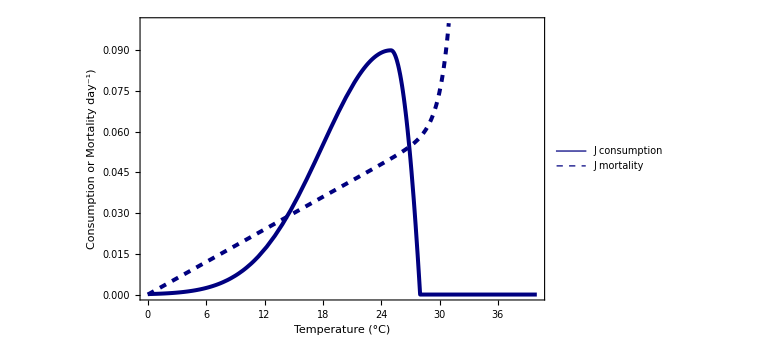

```mathematica
Plot[{awj[Tx]/.params,mj[Tx]/.params},{Tx,0,40}, PlotLegends->{"J consumption","J mortality"}, PlotRange->{{0,40},{0,0.1}}, Frame->True, 
FrameLabel->{{"Consumption or Mortality day^-1)",""},{"Temperature (°C)",""}}, PlotStyle ->{{Thickness[0.005],Darker[Blue,0.5]},{Thickness[0.005],Dashed,Darker[Blue,0.5]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

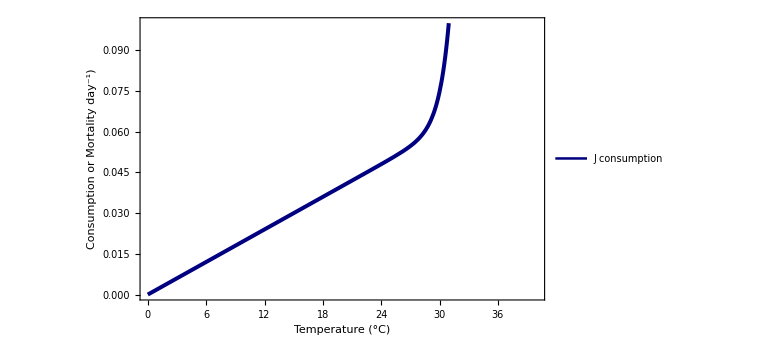

```mathematica
Plot[{mj[Tx]/.params/.σ2->5},{Tx,0,40}, PlotLegends->{"J consumption","J mortality"}, PlotRange->{{0,40},{0,0.1}}, Frame->True, 
FrameLabel->{{"Consumption or Mortality day^-1)",""},{"Temperature (°C)",""}}, PlotStyle ->{{Thickness[0.005],Darker[Blue,0.5]},{Thickness[0.005],Dashed,Darker[Blue,0.5]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### TPCs

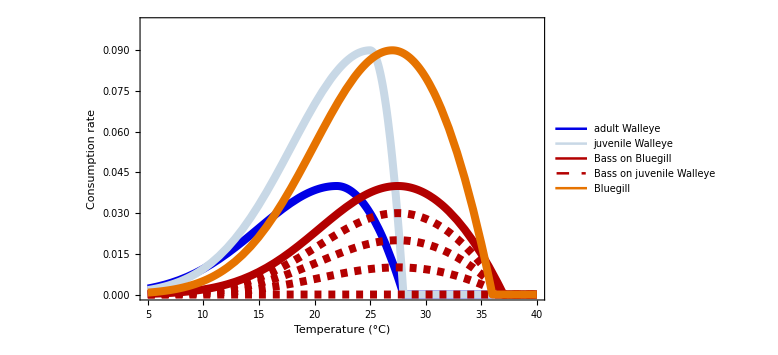

```mathematica
Plot[{awa[Tx]/.params, awj[Tx]/.params, aba[Tx]/.params, aba22[Tx]/.params, aba22[Tx]/.aba2->0.01/.params, aba22[Tx]/.aba2->0.02/.params, aba22[Tx]/.aba2->0.03/.params,ar2[Tx]/.params},{Tx,5,40}, PlotRange->{{5,40},{0,0.10}}, PlotLegends->{"adult Walleye", "juvenile Walleye", "Bass on Bluegill", "Bass on juvenile Walleye", "", "", "", "Bluegill"}, Frame->True, 
FrameLabel->{{"Consumption rate",""},{"Temperature (°C)",""}}, PlotStyle -> {{Thickness[0.01],Darker[Blue,0.1]},{Thickness[0.01],Darker[LightBlue,0.1]}, {Thickness[0.01], Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Darker[Orange,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

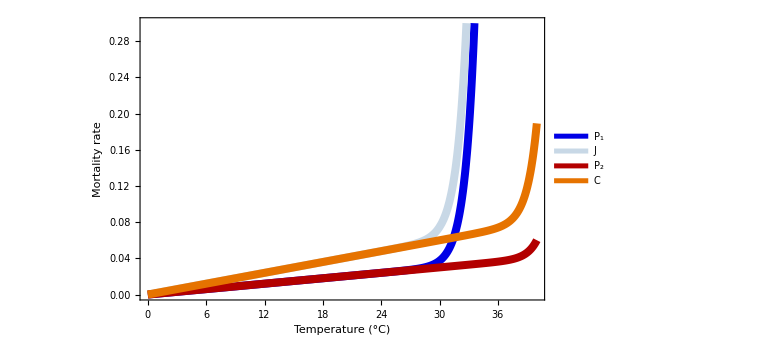

```mathematica
Plot[{ma[Tx]/.params, mj[Tx]/.params, mAb[Tx]/.params, mR2[Tx]/.params },{Tx,0,40}, PlotLegends->{"P_1","J","P_2","C"}, PlotRange->{{0,40},{0,0.3}}, Frame->True, 
FrameLabel->{{"Mortality rate",""},{"Temperature (°C)",""}}, PlotStyle ->{{Thickness[0.01],Darker[Blue,0.1]},{Thickness[0.01],Darker[LightBlue,0.1]}, {Thickness[0.01], Darker[Red,0.3]}, {Thickness[0.01], Darker[Orange,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

## Main Results

## A_1 & J are cool-water A_2 & R_2 are warm-water. A_1 and A_2 eat R_2 and R_2 and J eat R. No predation on J. In manuscript R_2 = C and A_1 and A_2 = P_1 and P_2.

## Biomass Trends

when mj = 0.005 & mR2=0.005, but the adults are both 0.001, you get the “expected result”

### P_1; T_max2 = 28

For this I changed aba2->0 to make sure I get the unexpected result and it worked, so I removed it again to get the alternate result. next scale from 0-0.4

```mathematica
Clear[bifMean28b]
bifMean28b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[A1h028b,A1h128b]
A1h028b =Take[bifMean28b[[All,2;;3]],{1,Length[bifMean28b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
A1h128b =Take[bifMean28b[[All,2;;3]],{2,Length[bifMean28b],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
A1h228b =Take[bifMean28b[[All,2;;3]],{3,Length[bifMean28b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
A1h328b =Take[bifMean28b[[All,2;;3]],{4,Length[bifMean28b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
A1h428b =Take[bifMean28b[[All,2;;3]],{5,Length[bifMean28b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

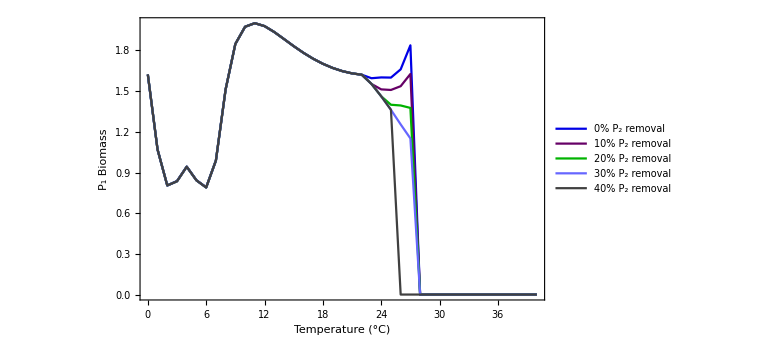

```mathematica
Clear[A1plot28b]
A1plot28b=ListLinePlot[{A1h028b,A1h128b,A1h228b,A1h328b,A1h428b}, PlotRange->{{0,40},All}, Frame->True, FrameLabel->{{"P_1 Biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"0% P_2 removal", "10% P_2 removal", "20% P_2 removal", "30% P_2 removal", "40% P_2 removal"},
PlotStyle -> {Darker[Blue,0.1],Darker[Purple,0.2],Darker[Green,0.3],Lighter[Blue,0.4],Darker[Gray,0.5]}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

```mathematica
A1h028b
```

{{0,0.942098},{1,1.16029},{2,0.876458},{3,0.476789},{4,0.681443},{5,0.698793},{6,0.613008},{7,0.963717},{8,1.23817},{9,1.78216},{10,1.95472},{11,1.99976},{12,1.98641},{13,1.94636},{14,1.89588},{15,1.84359},{16,1.79409},{17,1.74978},{18,1.71181},{19,1.68067},{20,1.6565},{21,1.63931},{22,1.62905},{23,1.60142},{24,1.61682},{25,1.60328},{26,1.66833},{27,1.84074},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
A1h428b
```

{{0,0.942074},{1,1.16023},{2,0.876536},{3,0.476893},{4,0.678071},{5,0.686233},{6,0.57305},{7,0.965259},{8,1.23686},{9,1.78211},{10,1.95472},{11,1.99976},{12,1.98641},{13,1.94636},{14,1.89588},{15,1.84359},{16,1.79409},{17,1.74978},{18,1.71181},{19,1.68067},{20,1.6565},{21,1.63931},{22,1.62886},{23,1.55083},{24,1.46017},{25,1.36092},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

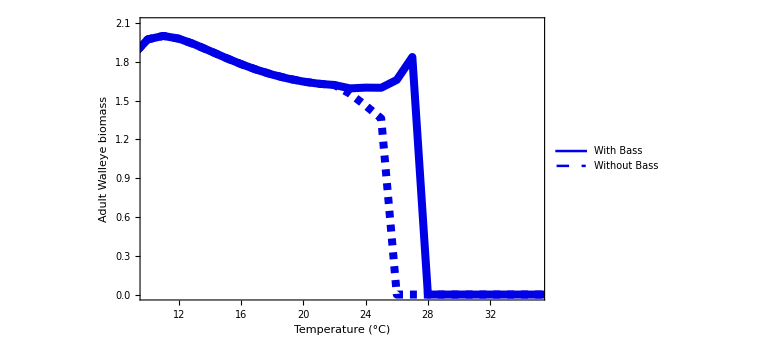

```mathematica
Clear[A1plot28b]
A1plot28b=ListLinePlot[{A1h028b,A1h428b}, PlotRange->{{10,35},{0,2.1}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

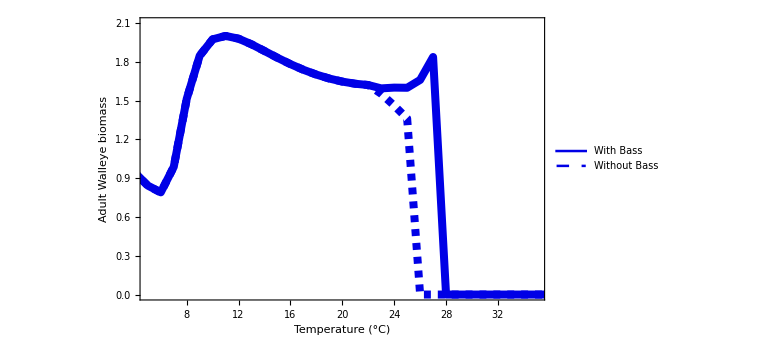

```mathematica
Clear[A1plot28b]
A1plot28b=ListLinePlot[{A1h028b,A1h428b}, PlotRange->{{5,35},{0,2.1}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

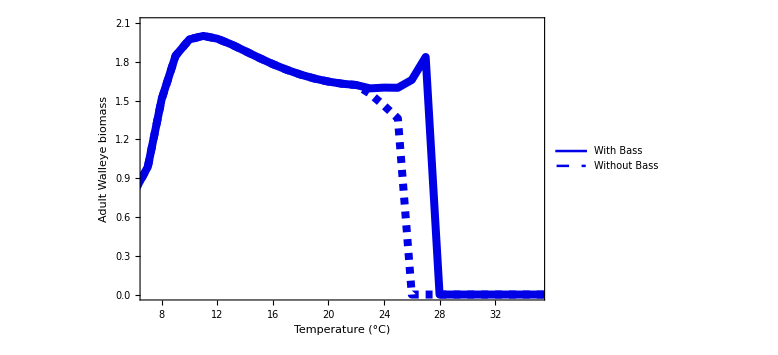

```mathematica
Clear[A1plot28b]
A1plot28b=ListLinePlot[{A1h028b,A1h428b}, PlotRange->{{7,35},{0,2.1}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### J_1; T_max2 = 28

```mathematica
Clear[bifMean28J1b]
bifMean28J1b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[J1[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[J1h028b,J1h128b]
J1h028b =Take[bifMean28J1b[[All,2;;3]],{1,Length[bifMean28J1b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
J1h128b =Take[bifMean28J1b[[All,2;;3]],{2,Length[bifMean28J1b],11}];
J1h228b =Take[bifMean28J1b[[All,2;;3]],{3,Length[bifMean28J1b],11}];
J1h328b =Take[bifMean28J1b[[All,2;;3]],{4,Length[bifMean28J1b],11}];
J1h428b =Take[bifMean28J1b[[All,2;;3]],{5,Length[bifMean28J1b],11}];
```

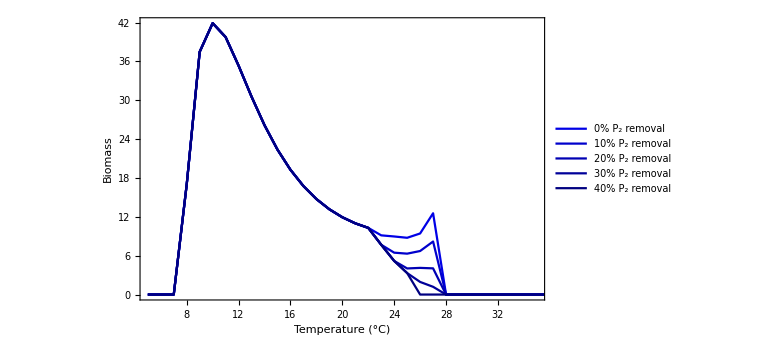

```mathematica
Clear[J1plot28b]
J1plot28b=ListLinePlot[{J1h028b,J1h128b,J1h228b,J1h328b,J1h428b}, PlotRange->{{5,35},All}, Frame->True, FrameLabel->{{"Biomass", ""}, {"Temperature (°C)", "cool-water juvenile biomass"}}, PlotLegends->{"0% P_2 removal", "10% P_2 removal", "20% P_2 removal", "30% P_2 removal", "40% P_2 removal"},
PlotStyle -> {Darker[Blue,0.1],Darker[Blue,0.2],Darker[Blue,0.3],Darker[Blue,0.4],Darker[Blue,0.5]}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

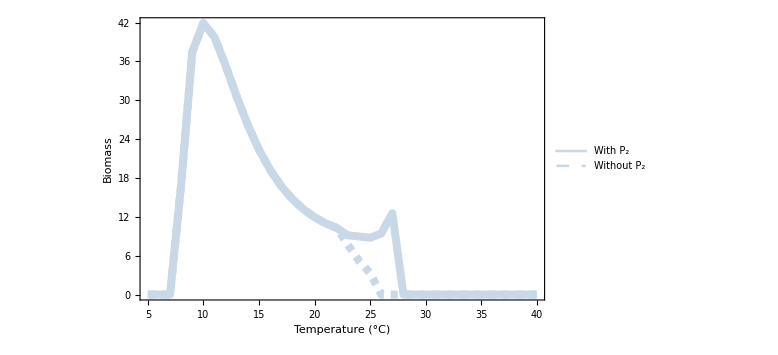

```mathematica
Clear[J1plot28b]
J1plot28b=ListLinePlot[{J1h028b,J1h428b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"Biomass", ""}, {"Temperature (°C)", "cool-water juvenile biomass"}}, PlotLegends->{"With P_2", "Without P_2"},
PlotStyle -> {{Thickness[0.01], Darker[LightBlue,0.1]}, {Thickness[0.01], Dashed, Darker[LightBlue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### P_2; T_max2 = 28

```mathematica
Clear[bifMean28A2b]
bifMean28A2b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[A2[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[A2h028b,A2h128b]
A2h028b =Take[bifMean28A2b[[All,2;;3]],{1,Length[bifMean28A2b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
A2h128b =Take[bifMean28A2b[[All,2;;3]],{2,Length[bifMean28A2b],11}]; 
A2h228b =Take[bifMean28A2b[[All,2;;3]],{3,Length[bifMean28A2b],11}];
A2h328b =Take[bifMean28A2b[[All,2;;3]],{4,Length[bifMean28A2b],11}]; 
A2h428b =Take[bifMean28A2b[[All,2;;3]],{5,Length[bifMean28A2b],11}];(*5 is h=0.2*)
```

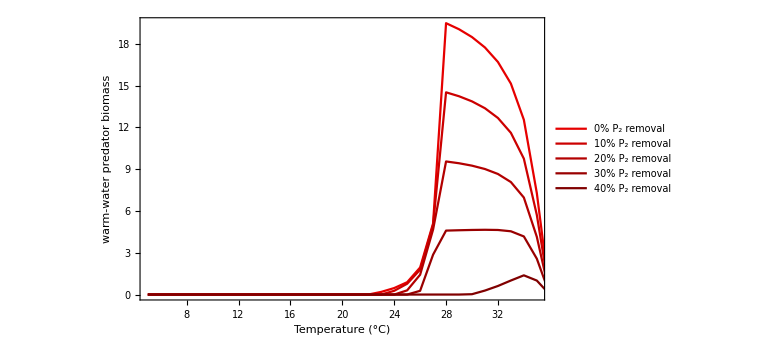

```mathematica
Clear[A2plot28b]
A2plot28b=ListLinePlot[{A2h028b,A2h128b,A2h228b,A2h328b,A2h428b}, PlotRange->{{5,35},All}, Frame->True, FrameLabel->{{"warm-water predator biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"0% P_2 removal", "10% P_2 removal", "20% P_2 removal", "30% P_2 removal", "40% P_2 removal"},
PlotStyle -> {Darker[Red,0.1],Darker[Red,0.2],Darker[Red,0.3],Darker[Red,0.4],Darker[Red,0.5]}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

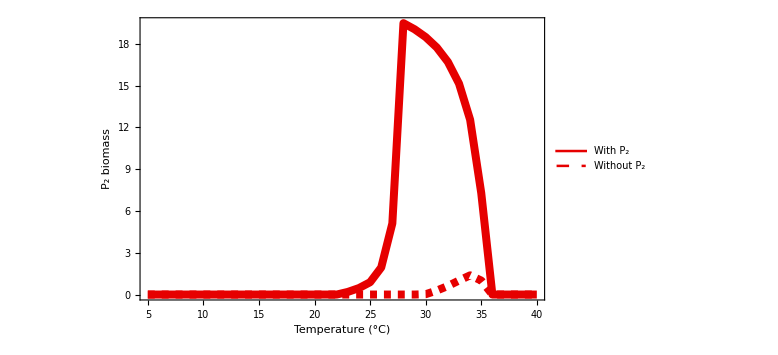

```mathematica
Clear[A2plot28b]
A2plot28b=ListLinePlot[{A2h028b,A2h428b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"P_2 biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With P_2", "Without P_2"},
PlotStyle -> {{Thickness[0.01],Darker[Red,0.1]},{Thickness[0.01],Dashed,Darker[Red,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### R_2; T_max2 = 28

```mathematica
Clear[bifMean28R2b]
bifMean28R2b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[R2[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[R2h028b,R2h128b]
R2h028b =Take[bifMean28R2b[[All,2;;3]],{1,Length[bifMean28R2b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
R2h128b =Take[bifMean28R2b[[All,2;;3]],{2,Length[bifMean28R2b],11}]; (*5 is h=0.4*)
R2h228b =Take[bifMean28R2b[[All,2;;3]],{3Length[bifMean28R2b],11}]; (*5 is h=0.4*)
R2h328b =Take[bifMean28R2b[[All,2;;3]],{4,Length[bifMean28R2b],11}]; (*5 is h=0.4*)
R2h428b =Take[bifMean28R2b[[All,2;;3]],{5,Length[bifMean28R2b],11}]; (*5 is h=0.4*)
```

Take::take: Cannot take positions 1353 through 11 in {{0,2.1556},{0,2.37542},{0,2.37565},{0,2.37573},{0,2.37577},{0,2.37579},{0,2.37581},{0,2.37582},{0,2.37583},{0,2.37583},«441»}.

```mathematica
R2h028b
```

{{0,2.1556},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.79351},{24,0.602368},{25,0.63572},{26,0.67844},{27,0.676691},{28,0.701948},{29,0.743546},{30,0.805828},{31,0.896786},{32,1.03165},{33,1.24163},{34,1.60052},{35,2.33159},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
R2h428b
```

{{0,2.37577},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,2.56025},{24,5.056},{25,6.89621},{26,10.5678},{27,10.4444},{28,10.5412},{29,10.8959},{30,11.5483},{31,12.4673},{32,13.9245},{33,16.2833},{34,20.4026},{35,28.8757},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
Log[0/0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

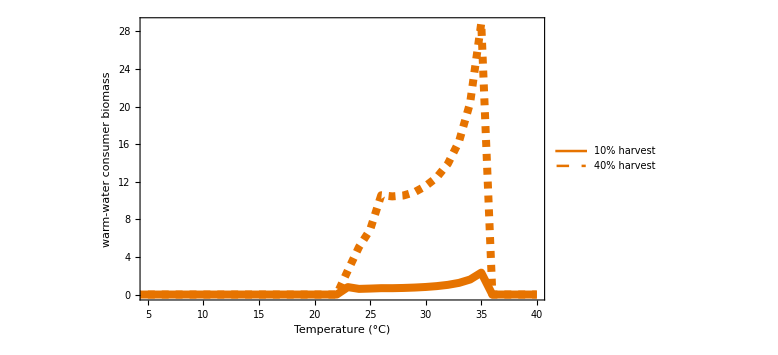

```mathematica
Clear[R2plot28b]
R2plot28b=ListLinePlot[{R2h028b,R2h428b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"warm-water consumer biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {{Thickness[0.01],Darker[Orange,0.1]},{Thickness[0.01],Dashed,Darker[Orange,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### R_1; T_max2 = 28

```mathematica
Clear[bifMean28R1b]
bifMean28R1b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[R1[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[R1h028b,R1h128b]
R1h028b =Take[bifMean28R1b[[All,2;;3]],{1,Length[bifMean28R1b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
R1h128b =Take[bifMean28R1b[[All,2;;3]],{2,Length[bifMean28R1b],11}];
R1h228b =Take[bifMean28R1b[[All,2;;3]],{3,Length[bifMean28R1b],11}];
R1h328b =Take[bifMean28R1b[[All,2;;3]],{4,Length[bifMean28R1b],11}];
R1h428b =Take[bifMean28R1b[[All,2;;3]],{5,Length[bifMean28R1b],11}]; (*5 is h=0.4*)
```

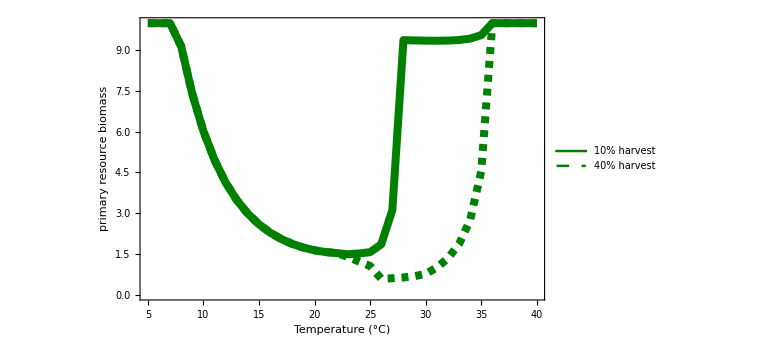

```mathematica
Clear[R1plot28b]
R1plot28b=ListLinePlot[{R1h028b,R1h428b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"primary resource biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {{Thickness[0.01],Darker[Green,0.5]},{Thickness[0.01],Dashed, Darker[Green,0.5]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### R_A1; T_max2 = 28

```mathematica
Clear[bifMean28RA1b]
bifMean28RA1b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.Tmax2->28/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[RA1[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[RA1h028,RA1h128]
RA1h028b =Take[bifMean28RA1b[[All,2;;3]],{2,Length[bifMean28RA1b],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
RA1h128b =Take[bifMean28RA1b[[All,2;;3]],{5,Length[bifMean28RA1b],11}]; (*5 is h=0.4*)
```

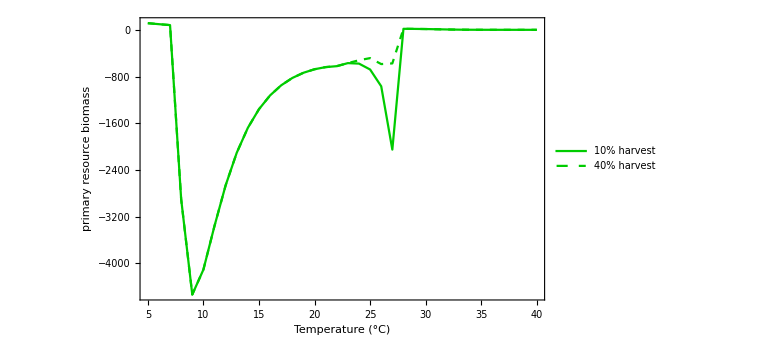

```mathematica
Clear[RA1plot28b]
RA1plot28b=ListLinePlot[{RA1h028b,RA1h128b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"primary resource biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {Darker[Green,0.2],{Dashed, Darker[Green,0.2]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### All; T_max2 = 28

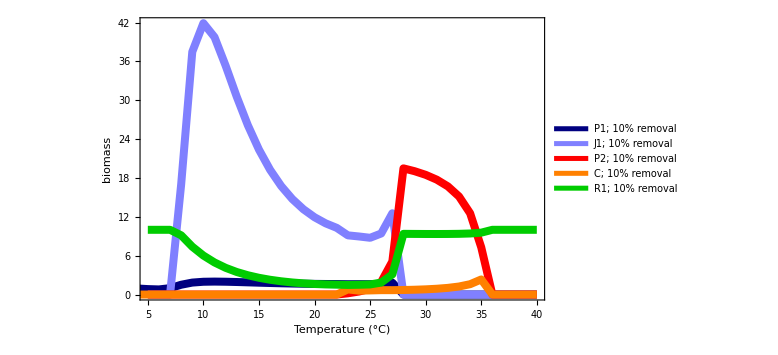

```mathematica
Clear[Allplot28b]
Allplot28b=ListLinePlot[{A1h028b,J1h028b,A2h028b,R2h028b,R1h028b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 10% removal","J1; 10% removal", "P2; 10% removal", "C; 10% removal", "R1; 10% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

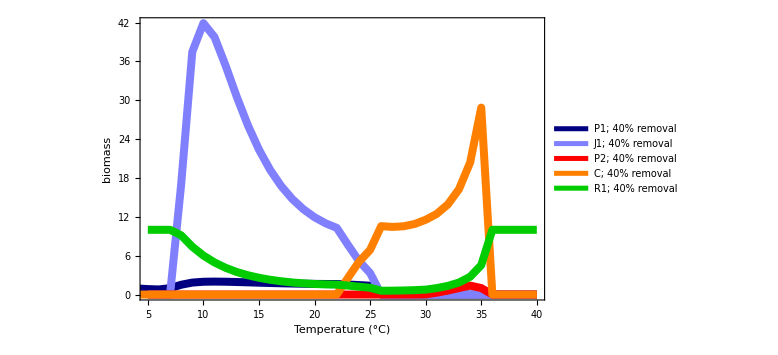

```mathematica
Clear[Allplot28]
Allplot28=ListLinePlot[{A1h428b,J1h428b,A2h428b,R2h428b,R1h428b}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 40% removal","J1; 40% removal", "P2; 40% removal", "C; 40% removal", "R1; 40% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

## P_1 Extinction Temperature - heat maps (sensitivity to various params)

### biomass, harvest, temp

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b]
biomP1b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{val,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b[[All,3]],_?NumberQ]]
```

1.83826

0

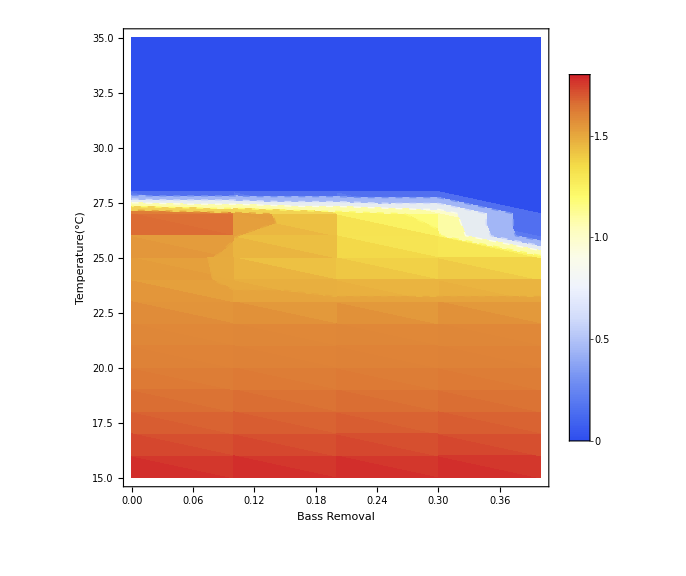

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot4]
plot4 = ListDensityPlot[biomP1b, 
Mesh->5,FrameLabel->{{"Temperature(°C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.8}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

### biomass, harvest, a

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b2]
biomP1b2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.aR21->aR21in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,aR21in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{aR21in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

The below is getting the maximum and minimum biomass estimates to set the temp colour range in the plot

```mathematica
Max@Cases[biomP1b2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b2[[All,3]],_?NumberQ]]
```

1.60012

1.36268

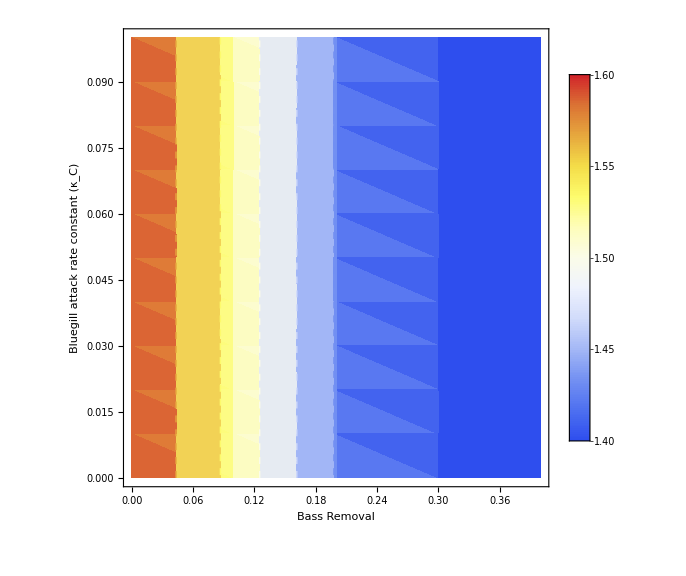

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot5]
plot5 = ListDensityPlot[biomP1b2, 
Mesh->5,FrameLabel->{{"Bluegill attack rate constant (κ_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.4,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b3]
biomP1b3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.awj1->awj1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,awj1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{awj1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b3[[All,3]],_?NumberQ]]
```

1.92562

0

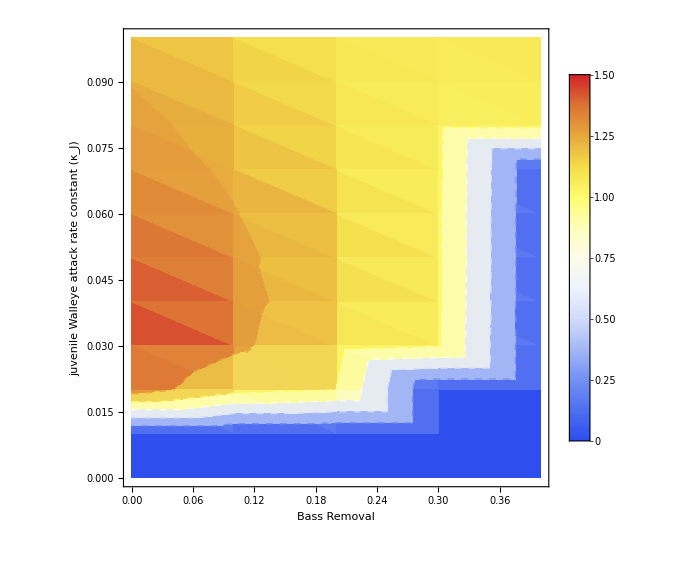

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot6]
plot6 = ListDensityPlot[biomP1b3, 
Mesh->5,FrameLabel->{{"juvenile Walleye attack rate constant (κ_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.5}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b4]
biomP1b4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.awa1->awa1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,awa1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{awa1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b4[[All,3]],_?NumberQ]]
```

1.63383

0

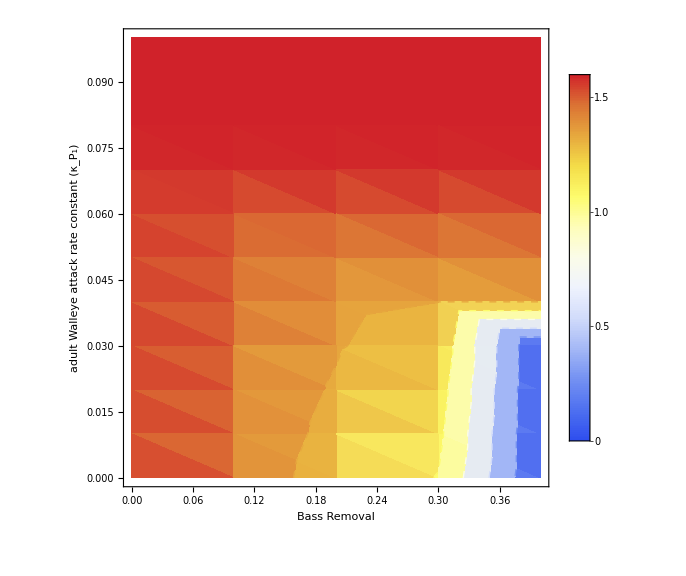

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot7]
plot7 = ListDensityPlot[biomP1b4, 
Mesh->5,FrameLabel->{{"adult Walleye attack rate constant (κ_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b5]
biomP1b5=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.aba1->aba1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,aba1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{aba1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b5[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b5[[All,3]],_?NumberQ]]
```

1.61858

1.36268

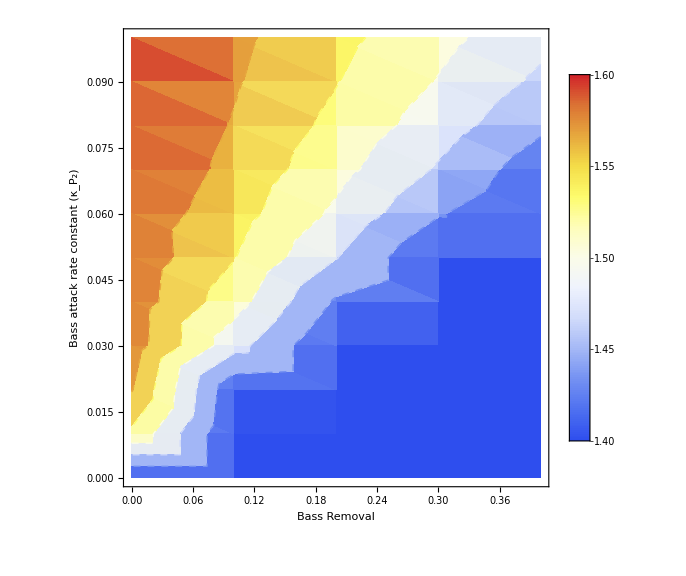

```mathematica
Clear[plot8]
plot8 = ListDensityPlot[biomP1b5, 
Mesh->5,FrameLabel->{{"Bass attack rate constant (κ_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.4,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

### biomass, harvest, m

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b6]
biomP1b6=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.ma1->ma1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,ma1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{ma1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b6[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b6[[All,3]],_?NumberQ]]
```

1.61742

1.08482

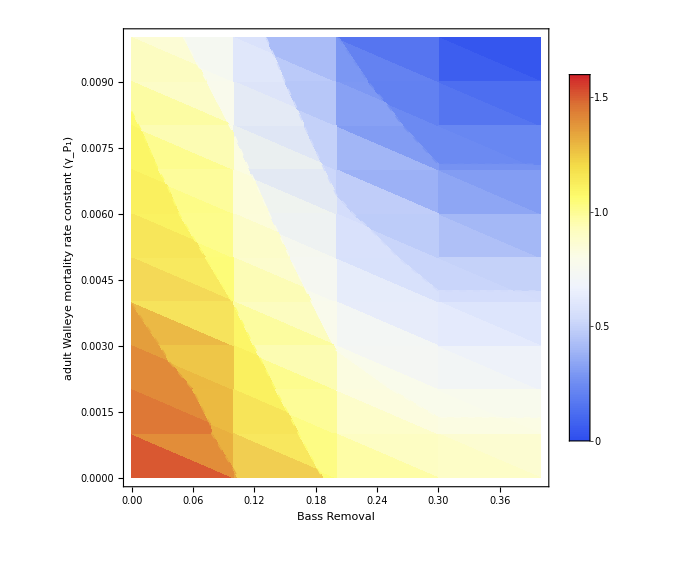

```mathematica
Clear[plot9]
plot9 = ListDensityPlot[biomP1b6, 
Mesh->5,FrameLabel->{{"adult Walleye mortality rate constant (γ_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b7]
biomP1b7=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.mj1->mj1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mj1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mj1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b7[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b7[[All,3]],_?NumberQ]]
```

1.92562

0

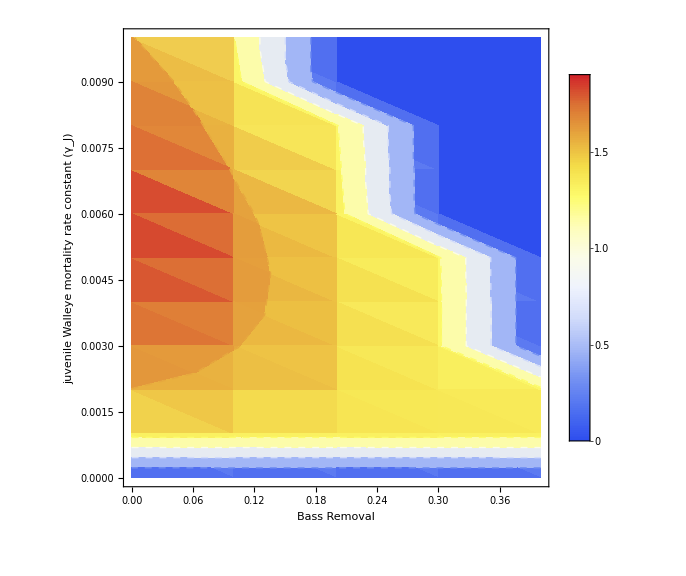

```mathematica
Clear[plot10]
plot10 = ListDensityPlot[biomP1b7, 
Mesh->5,FrameLabel->{{"juvenile Walleye mortality rate constant (γ_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.9}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b8]
biomP1b8=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.mAb1->mAb1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mAb1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mAb1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b8[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b8[[All,3]],_?NumberQ]]
```

1.63383

1.36268

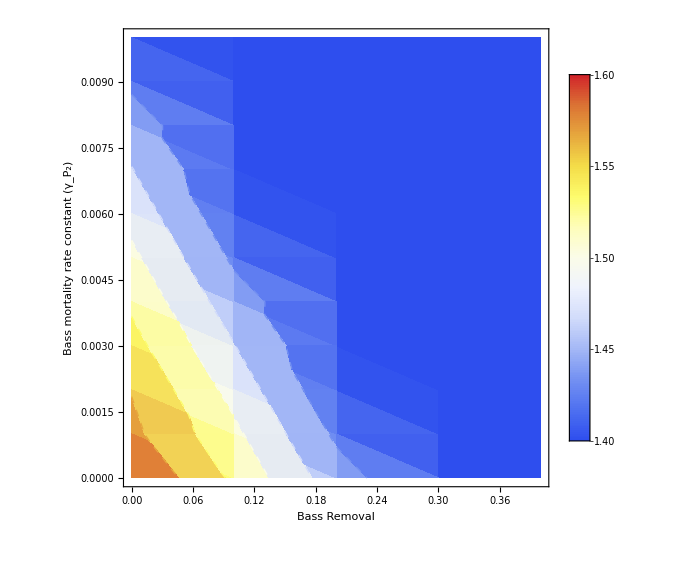

```mathematica
Clear[plot11]
plot11 = ListDensityPlot[biomP1b8, 
Mesh->5,FrameLabel->{{"Bass mortality rate constant (γ_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.4,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b9]
biomP1b9=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.mR21->mR21in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mR21in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mR21in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b9[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b9[[All,3]],_?NumberQ]]
```

1.63383

0

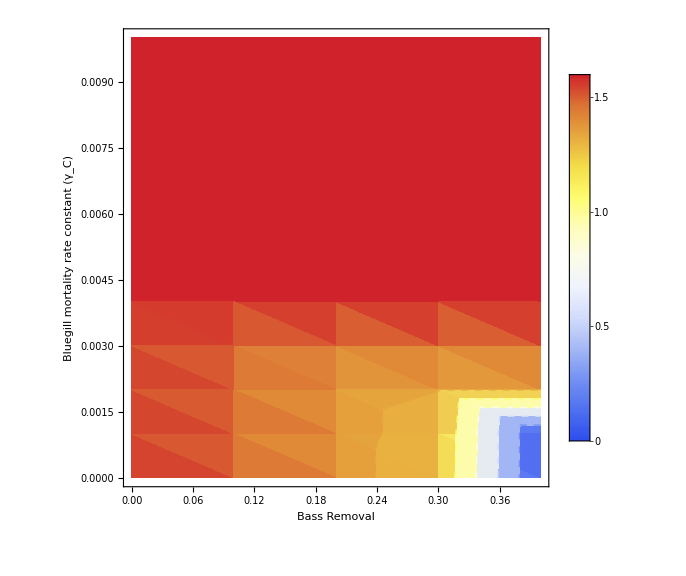

```mathematica
Clear[plot12]
plot12 = ListDensityPlot[biomP1b9, 
Mesh->5,FrameLabel->{{"Bluegill mortality rate constant (γ_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,1.60}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

### biomass, harvest, max temp

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b10]
biomP1b10=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.Tmax1->Tmax1in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax1in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax1in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b10[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b10[[All,3]],_?NumberQ]]
```

1.60973

1.30778

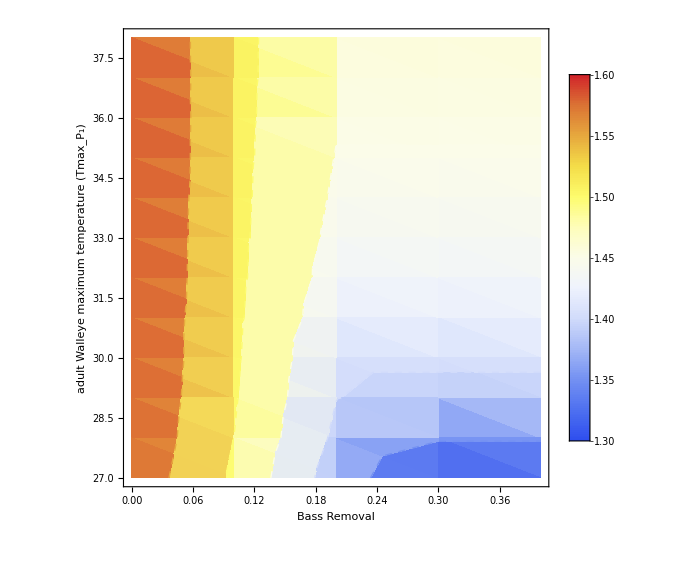

```mathematica
Clear[plot13]
plot13 = ListDensityPlot[biomP1b10, 
Mesh->5,FrameLabel->{{"adult Walleye maximum temperature (Tmax_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.3,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b11]
biomP1b11=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.Tmax2->Tmax2in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax2in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax2in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b11[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b11[[All,3]],_?NumberQ]]
```

1.60652

1.36213

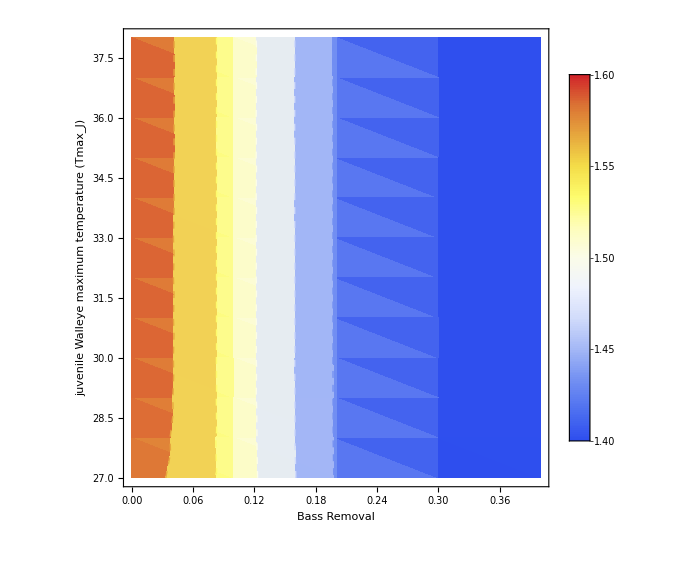

```mathematica
Clear[plot14]
plot14 = ListDensityPlot[biomP1b11, 
Mesh->5,FrameLabel->{{"juvenile Walleye maximum temperature (Tmax_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.4,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b12]
biomP1b12=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.Tmax3->Tmax3in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax3in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax3in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b12[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b12[[All,3]],_?NumberQ]]
```

1.60012

1.36268

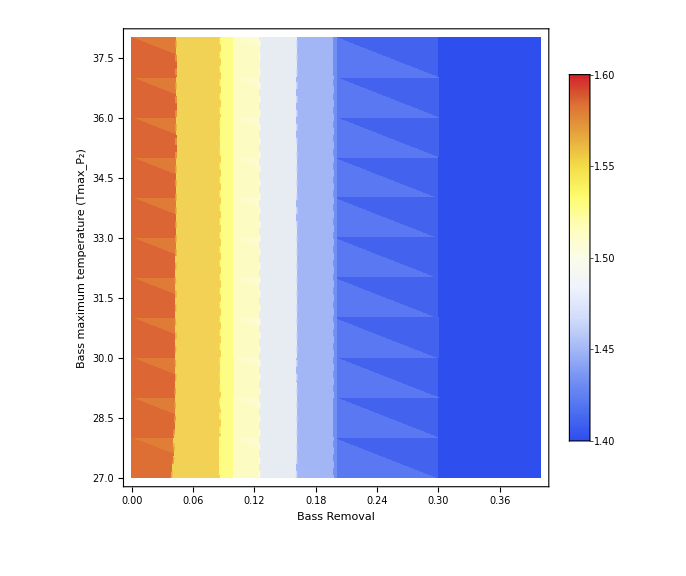

```mathematica
Clear[plot15]
plot15 = ListDensityPlot[biomP1b12, 
Mesh->5,FrameLabel->{{"Bass maximum temperature (Tmax_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.4,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b13]
biomP1b13=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.Tmax4->Tmax4in/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax4in,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax4in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b13[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b13[[All,3]],_?NumberQ]]
```

1.60791

1.36268

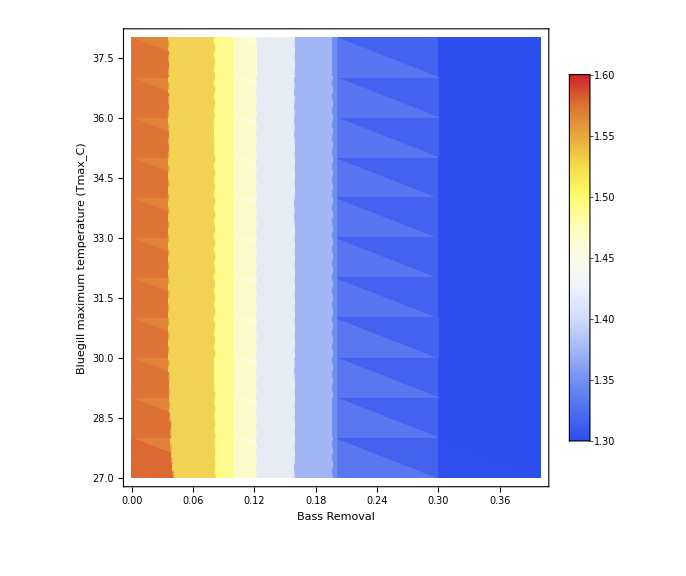

```mathematica
Clear[plot16]
plot16 = ListDensityPlot[biomP1b13, 
Mesh->5,FrameLabel->{{"Bluegill maximum temperature (Tmax_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{1.3,1.6}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

### biomass, harvest, maturity/somatic growth

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b14]
biomP1b14=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.som->somin/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,somin,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{somin,0.0,1,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b14[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b14[[All,3]],_?NumberQ]]
```

34.706

0

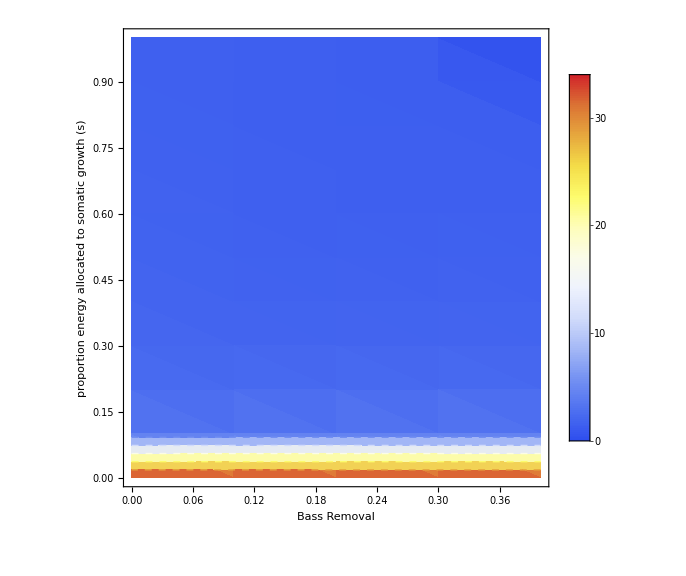

```mathematica
Clear[plot17]
plot17 = ListDensityPlot[biomP1b14, 
Mesh->5,FrameLabel->{{"proportion energy allocated to somatic growth (s)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,34.0}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b15]
biomP1b15=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.mat->matin/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,matin,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{matin,0.0,1,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b15[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b15[[All,3]],_?NumberQ]]
```

2.13622

0

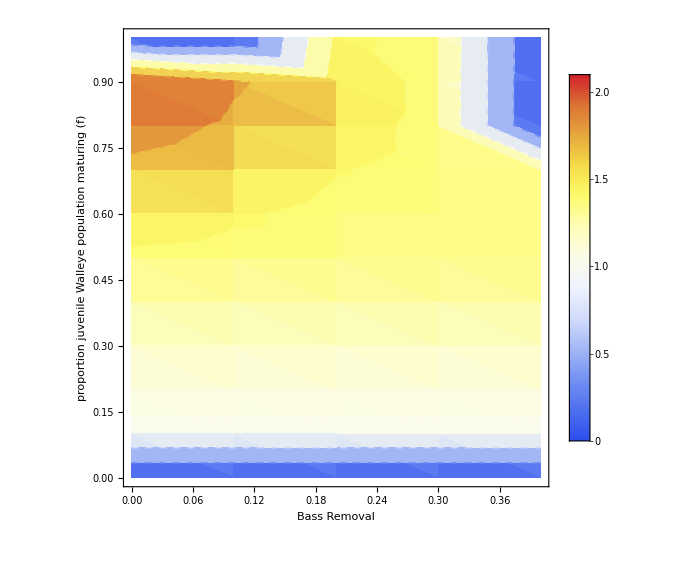

```mathematica
Clear[plot18]
plot18 = ListDensityPlot[biomP1b15, 
Mesh->5,FrameLabel->{{"proportion juvenile Walleye population maturing (f)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,2.1}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

## Cascades (log ratios )

### P_1; T_max2 = 28

with pred (h=0)

```mathematica
ratioP1pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[A1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
ratioP1npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[A1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logratiob28 =Transpose[{ratioP1pb28[[All,1]],Log[ratioP1pb28[[All,2]]/ratioP1npb28[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ratioP1npb28
```

{{10,1.97503},{11,2.00145},{12,1.97988},{13,1.93632},{14,1.88457},{15,1.83212},{16,1.78299},{17,1.73926},{18,1.70195},{19,1.67144},{20,1.64787},{21,1.6312},{22,1.62139},{23,1.55334},{24,1.4622},{25,1.36268},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
ratioP1pb28
```

{{10,1.97504},{11,2.00145},{12,1.97988},{13,1.93632},{14,1.88457},{15,1.83212},{16,1.78299},{17,1.73926},{18,1.70195},{19,1.67144},{20,1.64787},{21,1.6312},{22,1.62139},{23,1.5954},{24,1.60137},{25,1.60012},{26,1.66088},{27,1.83826},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
P1logratiob28
```

{{10,2.38753×10^-6},{11,3.51725×10^-7},{12,5.8344×10^-8},{13,1.04226×10^-8},{14,1.93349×10^-9},{15,3.66063×10^-10},{16,7.16565×10^-11},{17,1.49292×10^-11},{18,3.37397×10^-12},{19,7.74936×10^-13},{20,3.37508×10^-14},{21,-7.37521×10^-13},{22,-1.87079×10^-7},{23,0.0267126},{24,0.0909203},{25,0.160626},{26,∞},{27,∞},{28,Indeterminate},{29,Indeterminate},{30,Indeterminate},{31,Indeterminate},{32,Indeterminate},{33,Indeterminate},{34,Indeterminate},{35,Indeterminate},{36,Indeterminate},{37,Indeterminate},{38,Indeterminate},{39,Indeterminate},{40,Indeterminate}}

### J; T_max2 = 28

```mathematica
ratioJ1pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioJ1npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logratiob28=Transpose[{ratioJ1pb28[[All,1]],Log[ratioJ1pb28[[All,2]]/ratioJ1npb28[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### R_2; T_max2 = 28

p is with predator, np is no predator (no P2)

```mathematica
ratioR2pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R2[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioR2npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R2[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
R2logratiob28 =Transpose[{ratioR2pb28[[All,1]],Log[ratioR2pb28[[All,2]]/ratioR2npb28[[All,2]]]}] (*transpose is combining the first number for ratioR2p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioR2p and ratioR2np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{10,Indeterminate},{11,Indeterminate},{12,Indeterminate},{13,Indeterminate},{14,Indeterminate},{15,Indeterminate},{16,Indeterminate},{17,Indeterminate},{18,Indeterminate},{19,Indeterminate},{20,Indeterminate},{21,Indeterminate},{22,Indeterminate},{23,-1.17139},{24,-2.12746},{25,-2.38397},{26,-2.74577},{27,-2.73661},{28,-2.70919},{29,-2.68471},{30,-2.66242},{31,-2.63205},{32,-2.60249},{33,-2.57372},{34,-2.54534},{35,-2.51645},{36,Indeterminate},{37,Indeterminate},{38,Indeterminate},{39,Indeterminate},{40,Indeterminate}}

```mathematica
ratioR2pb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.79351},{24,0.602368},{25,0.63572},{26,0.67844},{27,0.676691},{28,0.701948},{29,0.743546},{30,0.805828},{31,0.896786},{32,1.03165},{33,1.24163},{34,1.60052},{35,2.33159},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
ratioR2npb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,2.56025},{24,5.056},{25,6.89621},{26,10.5678},{27,10.4444},{28,10.5412},{29,10.8959},{30,11.5483},{31,12.4673},{32,13.9245},{33,16.2833},{34,20.4026},{35,28.8757},{36,0},{37,0},{38,0},{39,0},{40,0}}

### R_1; T_max2 = 28

```mathematica
ratioR1pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioR1npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
R1logratiob28=Transpose[{ratioR1pb28[[All,1]],Log[(1+ratioR1pb28[[All,2]])/(1+ratioR1npb28[[All,2]])]}] ;
```

### All

Here, P1, J, and R1 have Log(Np2+/Np2-) close to zero because their biomass values are very similar (if not  exactly the same) so Log(1)=0. Whereas C biomass is zero until 22C.

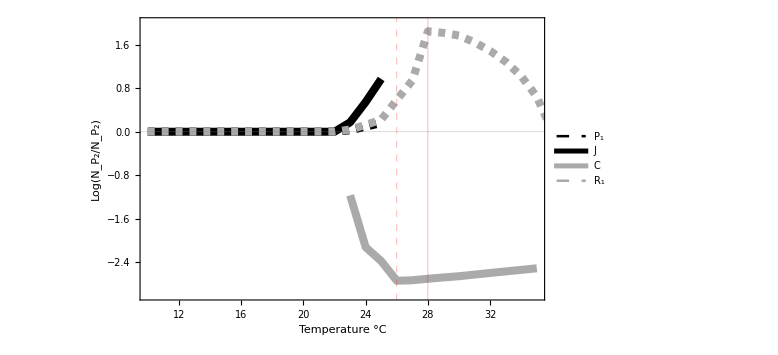

```mathematica
Show[
ListLinePlot[P1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Dashed,Black},PlotLegends->{"P_1"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logratiob28,  PlotRange->All, PlotStyle->{Thickness[0.01],Black},PlotLegends->{"J"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logratiob28,  PlotRange->All, PlotStyle->{Thickness[0.01],Lighter[Gray]},PlotLegends->{"C"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R1logratiob28,  PlotRange->All, PlotStyle->{Thickness[0.01],Dashed,Lighter[Gray]},PlotLegends->{"R_1"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{10,35},{-3,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_P_2/N_P_2)"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True, GridLines->{{{26,Directive[Thickness->.005,Dashed,Red]},{28,Directive[Thickness->.005,Red]}},{0}}, Axes->False
]
```

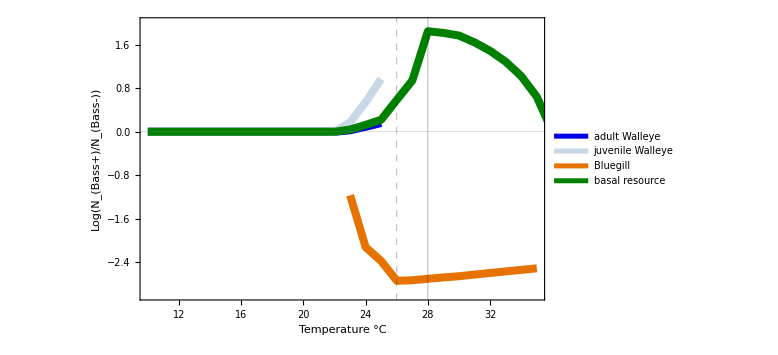

```mathematica
Show[
ListLinePlot[P1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Green, 0.5]},PlotLegends->{"basal resource"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{10,35},{-3,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True, GridLines->{{{26,Directive[Thickness->.005,Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

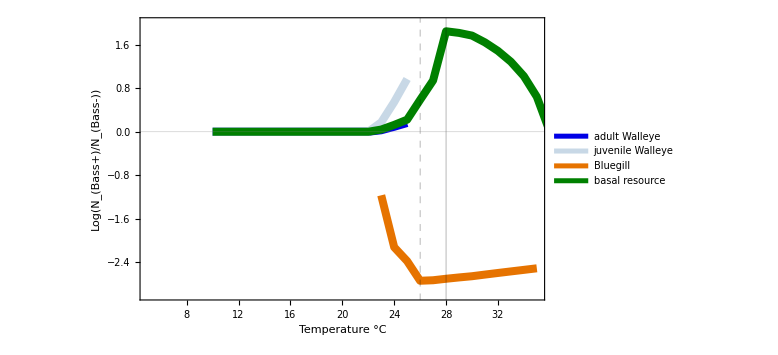

```mathematica
Show[
ListLinePlot[P1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Green, 0.5]},PlotLegends->{"basal resource"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{5,35},{-3,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True, GridLines->{{{26,Directive[Thickness->.005,Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

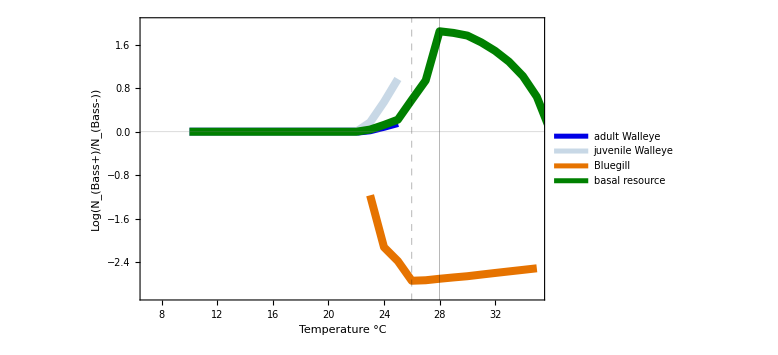

```mathematica
Show[
ListLinePlot[P1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R1logratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Green, 0.5]},PlotLegends->{"basal resource"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{7,35},{-3,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True, GridLines->{{{26,Directive[Thickness->.005,Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

## Cascades (log flux ratios)

### P_1; T_max2 = 28

with pred (h=0)

```mathematica
fratioP1pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[R2[Range[4000,5000]]]Mean[A1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
fratioP1npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[R2[Range[4000,5000]]]Mean[A1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logfratiob28=Transpose[{fratioP1pb28[[All,1]],Log[fratioP1pb28[[All,2]]/fratioP1npb28[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
P1logfratiob
```

P1logfratiob

### J; T_max2 = 28

```mathematica
fratioJ1pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioJ1npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logfratiob28=Transpose[{fratioJ1pb28[[All,1]],Log[fratioJ1pb28[[All,2]]/fratioJ1npb28[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### R_2; T_max2 = 28

p is with predator, np is no predator (no P2)

```mathematica
fratioR2pb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ar21*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[R2[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioR2npb28=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.Tmax2->28/.T1->val/.h->0.4/.T1->val/.rates/.params},{R1,R2,J1,A1,A2,RA1},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ar21*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[R2[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
R2logfratiob28 =Transpose[{fratioR2pb28[[All,1]],Log[fratioR2pb28[[All,2]]/fratioR2npb28[[All,2]]]}] ;(*transpose is combining the first number for ratioR2p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioR2p and ratioR2np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### All

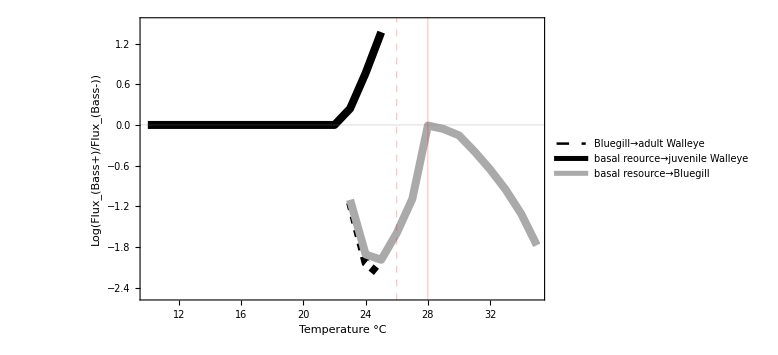

```mathematica
Show[
ListLinePlot[P1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Dashed,Black},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Black},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Lighter[Gray]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{10,35},{-2.5,1.5}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True , GridLines->{{{26,Directive[Thickness->.005, Dashed,Red]},{28,Directive[Thickness->.005,Red]}},{0}} , Axes->False
]
```

```mathematica
R2logfratiob28
```

{{10,Indeterminate},{11,Indeterminate},{12,Indeterminate},{13,Indeterminate},{14,Indeterminate},{15,Indeterminate},{16,Indeterminate},{17,Indeterminate},{18,Indeterminate},{19,Indeterminate},{20,Indeterminate},{21,Indeterminate},{22,Indeterminate},{23,-1.10348},{24,-1.90882},{25,-1.98799},{26,-1.59304},{27,-1.08991},{28,-0.00901025},{29,-0.0591642},{30,-0.153887},{31,-0.392253},{32,-0.655833},{33,-0.954915},{34,-1.31139},{35,-1.77309},{36,Indeterminate},{37,Indeterminate},{38,Indeterminate},{39,Indeterminate},{40,Indeterminate}}

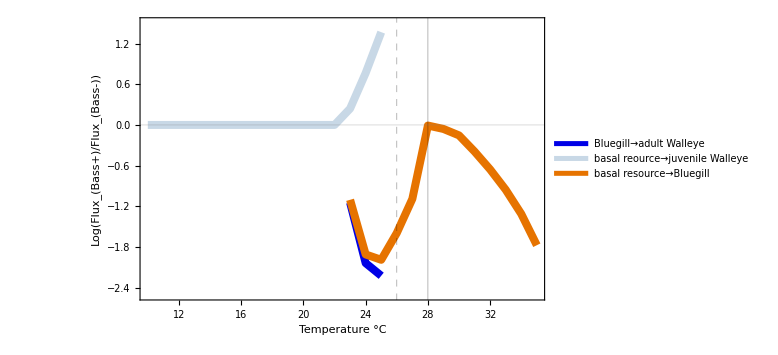

```mathematica
Show[
ListLinePlot[P1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{10,35},{-2.5,1.5}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True , GridLines->{{{26,Directive[Thickness->.005, Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

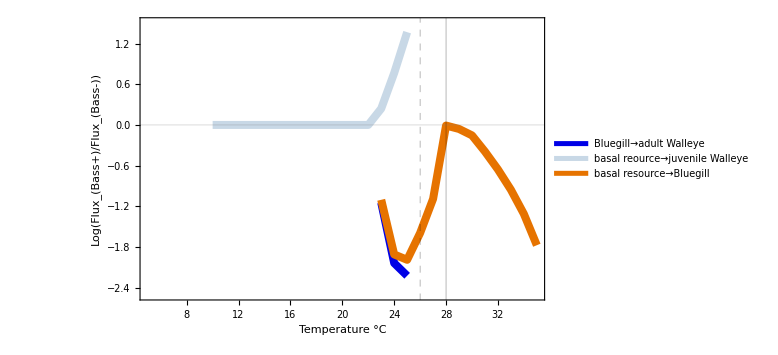

```mathematica
Show[
ListLinePlot[P1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{5,35},{-2.5,1.5}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True , GridLines->{{{26,Directive[Thickness->.005, Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

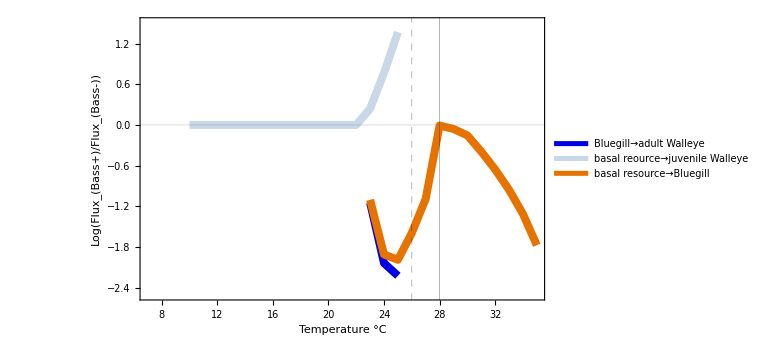

```mathematica
Show[
ListLinePlot[P1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],ListLinePlot[J1logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
ListLinePlot[R2logfratiob28, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]],
PlotRange->{{7,35},{-2.5,1.5}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"], Frame->True , GridLines->{{{26,Directive[Thickness->.005, Dashed,Black]},{28,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

```mathematica
fratioR2pb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.0903693},{24,0.0749495},{25,0.0858436},{26,0.111723},{27,0.189644},{28,0.585022},{29,0.595677},{30,0.603103},{31,0.60573},{32,0.600708},{33,0.582272},{34,0.536688},{35,0.421015},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
fratioR2npb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.27243},{24,0.505546},{25,0.62673},{26,0.549528},{27,0.564002},{28,0.590317},{29,0.631983},{30,0.703435},{31,0.89667},{32,1.15741},{33,1.51301},{34,1.99183},{35,2.47936},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
fratioP1pb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.0492319},{24,0.0342975},{25,0.0305169},{26,0.0250401},{27,0.0152037},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

```mathematica
fratioP1npb28
```

{{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0.154659},{24,0.262858},{25,0.28192},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

## P_1 Extinction Temperature

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanA1]
ExtMeanA1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.aba2->aba22/.T1->val/.h->hin/.params/.rates,{R1,R2,J1,A1,A2,RA1},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{aba22,hin,val,Chop[Mean[A1[Range[4000,5000]]]/.sol1,10^-2]}],{aba22,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanA1;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3.csv",ExtMeanA1,"Table"];
```

```mathematica
Clear[data1]
data1=Import["ext3.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each aba2 value (was Tmax value 28-35)*)
A1se1 =Drop[Cases[data1,{0.00,_,_,_}],None,1];
A1se2 =Drop[Cases[data1,{0.01,_,_,_}],None,1];
A1se3 =Drop[Cases[data1,{0.02,_,_,_}],None,1];
A1se4 =Drop[Cases[data1,{0.03,_,_,_}],None,1];
A1se5 =Drop[Cases[data1,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
A1ext1= Take[Table[FirstCase[A1se1,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
A1ext2= Take[Table[FirstCase[A1se2,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
A1ext3= Take[Table[FirstCase[A1se3,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
A1ext4= Take[Table[FirstCase[A1se4,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
A1ext5= Take[Table[FirstCase[A1se5,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

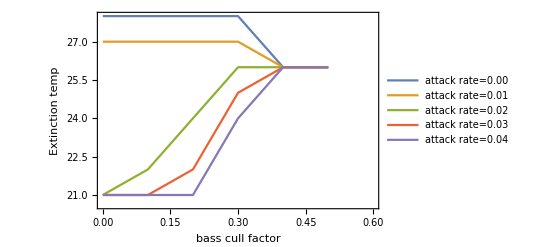

```mathematica
(*This is the line version of everything*)
A1plotA=ListLinePlot[{A1ext1,A1ext2,A1ext3,A1ext4,A1ext5}, PlotRange->{{0,0.6},All}, Frame->True, FrameLabel->{{"Extinction temp", ""}, {"bass cull factor", "(a) Cool-water predator"}}, PlotLegends->{"attack rate=0.00", "attack rate=0.01", "attack rate=0.02", "attack rate=0.03", "attack rate=0.04"}, LabelStyle->Directive[Medium]]
```

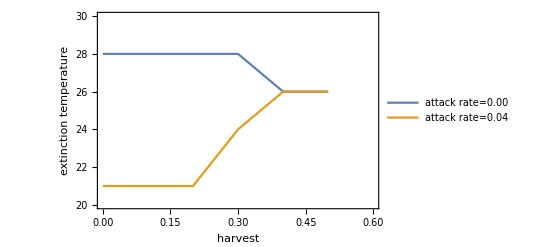

```mathematica
(*This is the line version of everything - condensed*) (*also, this is for cool-water predator when intermediate consumer is warm-water...used in MS*)
A1plotA2=ListLinePlot[{A1ext1,A1ext5}, PlotRange->{{0,0.6},{20,30}}, Frame->True, FrameLabel->{{"extinction temperature", ""}, {"harvest", ""}}, PlotLegends->{"attack rate=0.00", "attack rate=0.04"},LabelStyle->Directive[Bold, Medium]]
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.4)

```mathematica
(*This is where you start the heat map plot*)
A1x1 =Cases[data1,{0.00,_,_,_}];
A1x2 =Cases[data1,{0.01,_,_,_}];
A1x3 =Cases[data1,{0.02,_,_,_}];
A1x4 =Cases[data1,{0.03,_,_,_}];
A1x5 =Cases[data1,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.4. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
A1T1= Take[Table[FirstCase[A1x1,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
A1T2= Take[Table[FirstCase[A1x2,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
A1T3= Take[Table[FirstCase[A1x3,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
A1T4= Take[Table[FirstCase[A1x4,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
A1T5= Take[Table[FirstCase[A1x5,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1 = Join[A1T1,A1T2,A1T3,A1T4,A1T5];
Max[extdata1[[All,3]]]
Min[extdata1[[All,3]]]
```

```mathematica
°
```

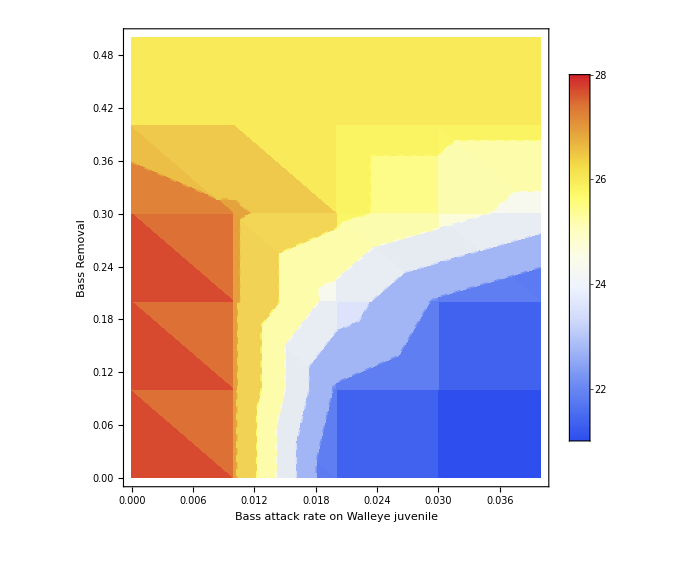

```mathematica
Clear[plot]
plot = ListDensityPlot[extdata1, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on Walleye juvenile"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{21,28}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->24,Bold,FontFamily->"Times"]]
```

## Time series

```mathematica
Manipulate[Module[{RA1sol,R1sol,R2sol,J1sol,A1sol,A2sol},
  {RA1sol,R1sol,R2sol,J1sol,A1sol,A2sol} = NDSolveValue[
  PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.params/.rates,
  {RA1,R1,R2,J1,A1,A2},{t,4000,5000}, MaxStepSize->0.05, MaxSteps->500000];
  Plot[{R1sol[t],R2sol[t],J1sol[t],A1sol[t],A2sol[t]},{t,4000,5000}, PlotStyle->{{Red,Dashed},{Blue,Dashed},Yellow, Green, Black, Pink, {Purple, Dashed}},PlotRange->All, PlotLegends-> "Expressions"]],
  {{T1in,25},15,40,2}
  ]
```

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rates} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolveValue::deqn: Equation or list of equations expected instead of PdSystem[{1.,1.,1.,1.,1.,1.}]/.params/.rates in the first argument PdSystem[{1.,1.,1.,1.,1.,1.}]/.params/.rates.

Set::shape: Lists {RA1sol$9736,R1sol$9736,R2sol$9736,J1sol$9736,A1sol$9736,A2sol$9736} and NDSolveValue[PdSystem[{1.,1.,1.,1.,1.,1.}]/.params/.rates,{RA1,R1,R2,J1,A1,A2},{t,4000,5000},MaxStepSize→0.05,MaxSteps→500000] are not the same shape.

```mathematica
sol=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25.0/.params/.rates,{RA1,R1,R2,J1,A1,A2},{t,4000,5000},AccuracyGoal->70,MaxStepSize->0.05,MaxSteps->500000];
```

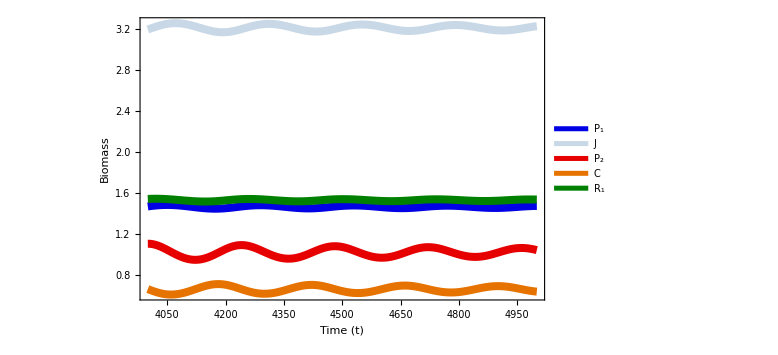

```mathematica
Plot[Evaluate[{A1[t],J1[t],A2[t],R2[t],R1[t]}/.sol],{t,4000,5000}, PlotLegends-> {"P_1","J","P_2","C","R_1"}, Frame->True, ImageSize->Large, 
PlotStyle->{{Thickness[0.01],Darker[Blue, 0.1]},{Thickness[0.01],Darker[LightBlue, 0.1]},{Thickness[0.01],Darker[Red, 0.1]},{Thickness[0.01],Darker[Orange, 0.1]},{Thickness[0.01],Darker[Green, 0.5]}},
FrameLabel->{"Time (t)","Biomass","",""},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

## Additional Notes

. increasing the difference in base attack rates for A1 and R2 (increasing R2 and decreasing A1), the time of walleye extinction for no bass harvest and full harvest switches. So A1 extinction at h=0 was lower than h = 1 when awa1 = 0.04 and ar2 = 0.06 but higher when awa = 0.01 and ar2  = 0.09